# CCBH-PLPP: k x minMass exclusion plots

Davi  C. Rodrigues (this code). October, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled black hole (general case)
DEBH = Dark energy coupled Black Hole (implies k = - 3w)
GBH = Growing BH, k is arbitrary and without direct dark energy impact.
m1 = primary (larger) mass of the BBH or NSBH pair.

Naming conventions:
All defined variables/functions start with lower case letter.
“I” at the end of a function name: interpolated version. 
“Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{"codes", "Directories.wl"}]];

(*
  Calling wl files
  ***************** 
*)

getCode["Constants.wl"];
baseSimPoints = 5 10^5; (*The base number of points to be simmulated for each dimension, commonly 10^5-10^7, depends on the purpose.*)

(*getCode["ObsDataPreparationGWTC-3.wl"]; *)
getCode["PowerLawPlusPeakDefinition.wl"];
getCode["Cosmology.wl"];
getCode["MassFactorCorrection.wl"];

Print["End of running wl files."];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

(*Better names: probSigma[nSigma_] and sigmaProb[prob_]*)

sigmaProb::usage = "sigmaProb[probability] yields the number of σ's for a given probability.";
sigmaProb[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[RealAbs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 0, 10}]
];

Clear[probSigma];
probSigma[n_] := probSigma[n] = NProbability[RealAbs[x] > n, x\[Distributed]NormalDistribution[]];
```

Starting Constants.wl:

Starting PowerLawPlusPeakDefinition.wl:

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

Starting Cosmology.wl:

tableZformation loaded.

Starting MassFactorCorrection.wl:

Base number of simmulated points per dimension (baseSimPoints):   500000

"dataM1Merger"  6.17769

End of running wl files.

## Exclusion plot k x MinMass using random PLPP parameters

Modified version of the MassFactorCorrection.wl code, to allow for parameter variation

```mathematica
minDelayTime = First[listDelayTime]; (*min delay time to be computed, it can be lower than tdmin0*)
maxDelayTime[zObs_, tdmax_?NumberQ, zMax_?NumberQ, w_] := maxDelayTime[zObs, tdmax, zMax, w] = Min[
  tdmax,
  timeZ[zObs, zMax, w]
]; 

massFactor[zObs_,zFormation_, k_] = ((1 + zFormation)/(1 + zObs))^k; (*(a/a_i)^k. This is the factor that corrects the mass*)

SetAttributes[massFactorDelay, Listable];
massFactorDelay[zObs_, delayTime_, k_, zMax_, w_] =  massFactor[zObs, zFormationI[zObs, delayTime, zMax, w], k];

randomLogDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_, realizations_] := randomLogDelayTime[zObs, tdmin, tdmax,  zMax, w, realizations] = 
 RandomReal[{Log10[tdmin], Log10 @ maxDelayTime[zObs, tdmax, zMax, w]}, realizations]; (*log-flat distribution.*)

dataDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_] := dataDelayTime[zObs, tdmin, tdmax, zMax, w] = 
 10^randomLogDelayTime[zObs, tdmin, tdmax, zMax, w,  baseSimPoints]; 

dataMassFactor[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := dataMassFactor[zObs, tdmin, tdmax, k, zMax, w] = 
 massFactorDelay[zObs, dataDelayTime[zObs, tdmin, tdmax, zMax, w], k, zMax, w];
```

```mathematica
Clear[ 
  iPS, 
  cPI,  
  probabilityMminApprox, 
  probabilityMminApproxF
];

assoSamplesPLPPraw = Import[FileNameJoin[{pathIn, "all_samples_PLPP_GWTC3.h5"}], "Data"]; (*Data imported as association, asso for short.*)
assoSamplesPLPP = KeyMap[StringDelete[#, {"/", "_"}] & , assoSamplesPLPPraw]; (*Removes inconvenient strings from the key names.*) 

alpha = assoSamplesPLPP["alpha"];
beta = assoSamplesPLPP["beta"];
mmax = assoSamplesPLPP["mmax"];
mmin = assoSamplesPLPP["mmin"];
lam = assoSamplesPLPP["lam"];
mpp = assoSamplesPLPP["mpp"];
sigpp = assoSamplesPLPP["sigpp"];
deltam = assoSamplesPLPP["deltam"];

lengthSample = Length @ alpha;

Clear[𝒟plppR];
listRandomSample = RandomSample[Range @ lengthSample];
iPS[i_] := listRandomSample[[i]]; (*iPS is indexed PLPP Sample*)
cPI = 1; (*cPI is countPlppIndex*)
𝒟plppR := (
  (*cPI = cPI + 1;*)
  (*If[cPI > Length @ alpha, Echo["cPI exceeded."]; cp1 = 1];*)
  plpp`dist[
    plpp`a -> alpha[[iPS[cPI]]],
    plpp`mMin -> mmin[[iPS[cPI]]],
    plpp`dm -> deltam[[iPS[cPI]]],
    plpp`mMax -> mmax[[iPS[cPI]]],
    plpp`mu -> mpp[[iPS[cPI]]],
    plpp`s -> sigpp[[iPS[cPI]]],
    plpp`l -> lam[[iPS[cPI]]],
    plpp`betaQ -> beta[[iPS[cPI]]]
  ]
); (*
  𝒟plppR picks a random realization of the PLPP parameters (it never picks a realization more than once). 
  plpp`dist is defined in PowerLawPlusPeakDefinition.wl.
*)

(*To refresh all the definitions related to the massFactor*)
getCode["MassFactorCorrection.wl"]; (*It computes automatically a dataM1merger but it will not be used.*)

Clear[
  dataM1Merger, 
  dataDelayTime, 
  dataM1FormationRaw, 
  𝒟M1FormationEmpRaw, 
  𝒟M1FormationEmp
];

dataDelayTime[zObs_, tdmin_, tdmax_, zMax_, w_] := dataDelayTime[zObs, tdmin, tdmax, zMax, w] = 
 10^randomLogDelayTime[zObs, tdmin, tdmax, zMax, w,  baseSimPoints]; (*Redefined here to use baseSimPoints.*)

dataM1Merger[cpi_] := dataM1Merger[cpi] = Block[{cPI}, cPI = cpi; RandomVariate[𝒟plppR, baseSimPoints]];  (*2 baseSimPoints is not necessary here*)

dataM1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_, cpi_]:= 
 dataM1Merger[cpi] / dataMassFactor[zObs, tdmin, tdmax, 1, zMax, w]^k;

𝒟M1FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_, cpi_] := 
 EmpiricalDistribution[
   dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w, cpi]
 ];

𝒟M1FormationEmp[zObs_, cpi_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w,
  cpi
];

probabilityMminApprox[mMin_, cpi_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, cpi, opts], mMin]^72;
probabilityMminApproxF[mMin_, cpi_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, cpi, opts], mMin]^250; (*forecast*)
```

Starting MassFactorCorrection.wl:

Base number of simmulated points per dimension (baseSimPoints):   500000

"dataM1Merger"  12.1117

### Code for arbitrary cPI value

```mathematica
Clear[tab, sol, solAll, probValue];

probValue = probSigma[2];
listk1 = Range[0.5, 3, 0.1];
listm1 = Range[0.4, 6, 0.1];
sol[0, cpi_] = {arbitraryK, Last @ listm1}; (*Only used for the first step.*)

tab[nk1_, cpi_] := tab[nk1, cpi] = Block[{nm1Previous, nm1Minimal, listm1Relevant},
  nm1Previous = Position[listm1, Last@sol[nk1-1, cpi]][[1,1]];
  nm1Minimal = If[nm1Previous - 10 < 1, 1, nm1Previous - 10];
  listm1Relevant = listm1 // Take[#, {nm1Minimal, nm1Previous}] &;
  Table[
    {{listk1[[nk1]], m1}, Abs[probabilityMminApprox[m1, cpi, k -> listk1[[nk1]]] - probValue]} , 
    {m1, listm1Relevant}
  ]
];
sol[nk1_, cpi_] := sol[nk1, cpi] = tab[nk1, cpi] // SortBy[#, Last][[1,1]] & (*// Echo*);

solAll[cpi_] := solAll[cpi] = Monitor[Table[sol[nk1, cpi], {nk1, Length @ listk1}], {nk1, Length @ listk1}];
```

### Curves for 300 PLPP realizations

```mathematica
(*table300 = Table[solAll[cpi], {cpi, 1, 300}];*)
(*exportAux["listRandomSample.csv", listRandomSample]*)
(*exportAux["table300.json", table300]
dumpsave["table300.mx", table300]*)
getAux["table300.mx"]
```

```mathematica
dataKxM95 = {listk1[[#]], Quantile[table300[[All, # , 2]], 0.95]} & /@ (Range @ Length @ listk1);
dataKxM50 = {listk1[[#]], Quantile[table300[[All, # , 2]], 0.50]} & /@ (Range @ Length @ listk1);
dataKxM05 = {listk1[[#]], Quantile[table300[[All, # , 2]], 0.05]} & /@ (Range @ Length @ listk1);

kXm95I = Interpolation[dataKxM95, InterpolationOrder->2, Method->"Spline" ];
kXm50I = Interpolation[dataKxM50, InterpolationOrder->2, Method->"Spline"];
kXm05I = Interpolation[dataKxM05, InterpolationOrder->2, Method->"Spline"];
```

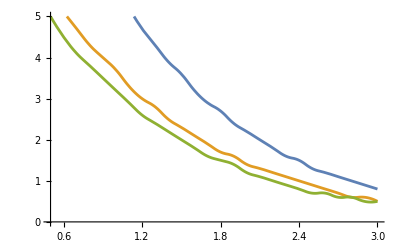

```mathematica
Plot[{kXm95I[k], kXm50I[k], kXm05I[k]}, {k,0.5, 3}, PlotRange->{{0.5, 3}, {0,5}}]
```

### Code for arbitrary cPI value - Forecast

```mathematica
Clear[tabF, solF, solAllF];

probValue = probSigma[2];
listk1 = Range[0.5, 3, 0.1];
listm1 = Range[0.1, 5.0, 0.1]; (*For the Forecast, minimmal mass = 0.1 and maximum 5.0.*)
solF[0, cpi_] = {arbitraryK, Last @ listm1}; (*Only used for the first step.*)

tabF[nk1_, cpi_] := tabF[nk1, cpi] = Block[{nm1Previous, nm1Minimal, listm1Relevant},
  nm1Previous = Position[listm1, Last @ solF[nk1-1, cpi]][[1,1]];
  nm1Minimal = If[nm1Previous - 10 < 1, 1, nm1Previous - 10]; 
  listm1Relevant = listm1 // Take[#, {nm1Minimal, nm1Previous}] &;
  Table[
    {{listk1[[nk1]], m1}, Abs[probabilityMminApproxF[m1, cpi, k -> listk1[[nk1]]] - probValue]} , 
    {m1, listm1Relevant}
  ]
];
solF[nk1_, cpi_] := solF[nk1, cpi] = tabF[nk1, cpi] // SortBy[#, Last][[1,1]] & (*// Echo*);

solAllF[cpi_] := solAllF[cpi] = Monitor[Table[solF[nk1, cpi], {nk1, Length @ listk1}], {nk1, Length @ listk1}];
```

```mathematica
(*table300F = Monitor[Table[solAllF[cpi], {cpi, 1, 300}], cpi];
exportAux["table300F.json", table300F]
dumpsave["table300F.mx", table300F]*)
getAux["table300F.mx"]
```

### Plotting all the results

```mathematica
dataKxM95F = {listk1[[#]], Quantile[table300F[[All, # , 2]], 0.95]} & /@ (Range @ Length @ listk1);
dataKxM50F = {listk1[[#]], Quantile[table300F[[All, # , 2]], 0.50]} & /@ (Range @ Length @ listk1);
dataKxM05F = {listk1[[#]], Quantile[table300F[[All, # , 2]], 0.05]} & /@ (Range @ Length @ listk1);

kXm95FI = Interpolation[dataKxM95F, InterpolationOrder->2, Method->"Spline" ];
kXm50FI = Interpolation[dataKxM50F, InterpolationOrder->2, Method->"Spline"];
kXm05FI = Interpolation[dataKxM05F, InterpolationOrder->2, Method->"Spline"];
```

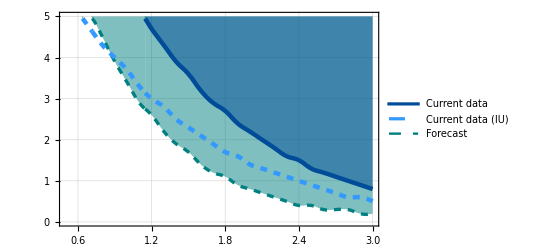

pathOut/plotkXmPLPP.pdf

```mathematica
color1i = RGBColor[0, 76/255, 153/255];
color1ii = RGBColor[51/255, 153/255, 255/255];
color1iii = RGBColor[153/255, 0, 0];
color1iv = RGBColor[255/255, 102/255, 102/255];
color3i = RGBColor[0, 128/255, 128/255];
color3ii = RGBColor[0, 192/255, 192/255];

legend = LineLegend[
  {
    Directive[Thickness[0.008], color1i],
    Directive[Thickness[0.008], color1ii, Dashing[Small]], 
    Directive[Thickness[0.006], color3i, Dashed]
    (*Directive[Thickness[0.006], color3ii, DotDashed]*)
  },
  {
    Style["Current data", FontFamily->"Times", FontSize -> 14],
    Style["Current data (IU)", FontFamily->"Times", FontSize -> 14], 
    Style["Forecast", FontFamily->"Times", FontSize -> 14]
    (*Style["Forecast (IU)", FontFamily->"Times", FontSize -> 14]*)
  },    
  LegendMarkerSize->{25, 5}
  (*Spacings -> 0.5*)
];

plotkXmPLPP = Plot[
  {
    If[kXm95FI[k]>=4.95, 200, kXm95FI[k]], 
    (*If[kXm50FI[k]>=4.95, 200, kXm50FI[k]],*)
    If[kXm95I[k]>=4.95, 200,kXm95I[k]], 
    If[kXm50I[k]>=4.95, 200, kXm50I[k]]
  }, 
  {k,0.5, 3}, 
  PlotRange->{{0.5, 3}, {0,5}},
  PlotStyle -> {
    {Thickness[0.006], color3i, Dashed},
    (*{Thickness[0.006], color3ii, DotDashed},*)
    {Thickness[0.008], color1i}, 
    {Thickness[0.008], color1ii, Dashing[Small]}
  },
  Background -> White,
  Frame -> True,
  Axes -> False,
  Filling->{1-> {Top, Directive[Opacity[0.5], color3i]}, (*2-> None,*) 2-> {Top, Directive[Opacity[0.5], color1i]}, 3-> None},
  FrameStyle-> Directive[Black, FontSize -> 13, FontFamily-> "Times"],
  FrameTicksStyle -> Directive[Black],
  GridLines->(*{{1.65, 2.1}, {}}*)Automatic,
  MaxRecursion->10,
  Epilog->Inset[legend, Scaled[{0.22,0.18}]]
]

exportOut["plotkXmPLPP.pdf", plotkXmPLPP]
```

```mathematica
Dashing
```

## EXTRA: Exclusion plot k x MinMass using best fit PLPP parameters: This is code part is valid only as a cross check. It yields the same result of the median

here I have to select randomly different PLPP values and find the probability with reference values.

```mathematica
𝒟M1FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 
 EmpiricalDistribution[
   dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w]
 ];

𝒟M1FormationEmp[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^72;
probabilityMminApproxF[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^250; (*forecast*)
```

```mathematica
probabilityMminApprox[2] // EchoTiming
```

0.167524

0.000236607

```mathematica
Clear[tab, sol, solAll, probValue];
probValue = probSigma[2];
listk1 = Range[0.5, 3, 0.025];
listm1 = Range[0.4, 6, 0.025];
sol[0] = {arbitraryK, Last @ listm1}; (*Only used for the first step.*)

tab[nk1_] := tab[nk1] = Block[{nm1Previous, nm1Minimal, listm1Relevant},
  nm1Previous = Position[listm1, Last@sol[nk1-1]][[1,1]];
  nm1Minimal = If[nm1Previous - 10 < 1, 1, nm1Previous - 10];
  listm1Relevant = listm1 // Take[#, {nm1Minimal, nm1Previous}] &;
  Table[
    {{listk1[[nk1]], m1}, Abs[probabilityMminApprox[m1, k -> listk1[[nk1]]] - probValue]} , 
    {m1, listm1Relevant}
  ]
];
sol[nk1_] := sol[nk1] = tab[nk1] // SortBy[#, Last][[1,1]] & (*// Echo*);

solAll := solAll = Monitor[Table[sol[nk1], {nk1, Length @ listk1}], nk1];
```

```mathematica
sol[2]
```

{5.65,0.525}

```mathematica
Reverse /@ solAll (*This solAll was generated with an inversed k x m position.*)
```

{{0.5,5.775},{0.525,5.65},{0.55,5.55},{0.575,5.425},{0.6,5.325},{0.625,5.2},{0.65,5.1},{0.675,4.975},{0.7,4.875},{0.725,4.775},{0.75,4.675},{0.775,4.575},{0.8,4.475},{0.825,4.375},{0.85,4.275},{0.875,4.175},{0.9,4.075},{0.925,4.},{0.95,3.9},{0.975,3.8},{1.,3.725},{1.025,3.65},{1.05,3.55},{1.075,3.475},{1.1,3.4},{1.125,3.325},{1.15,3.25},{1.175,3.175},{1.2,3.1},{1.225,3.025},{1.25,2.95},{1.275,2.875},{1.3,2.8},{1.325,2.75},{1.35,2.675},{1.375,2.625},{1.4,2.55},{1.425,2.5},{1.45,2.425},{1.475,2.375},{1.5,2.325},{1.525,2.25},{1.55,2.2},{1.575,2.15},{1.6,2.1},{1.625,2.05},{1.65,2.},{1.675,1.95},{1.7,1.9},{1.725,1.85},{1.75,1.8},{1.775,1.775},{1.8,1.725},{1.825,1.675},{1.85,1.65},{1.875,1.6},{1.9,1.575},{1.925,1.525},{1.95,1.475},{1.975,1.45},{2.,1.425},{2.025,1.375},{2.05,1.35},{2.075,1.325},{2.1,1.275},{2.125,1.25},{2.15,1.225},{2.175,1.2},{2.2,1.15},{2.225,1.125},{2.25,1.1},{2.275,1.075},{2.3,1.05},{2.325,1.025},{2.35,1.},{2.375,0.975},{2.4,0.95},{2.425,0.925},{2.45,0.9},{2.475,0.875},{2.5,0.85},{2.525,0.85},{2.55,0.825},{2.575,0.8},{2.6,0.775},{2.625,0.75},{2.65,0.75},{2.675,0.725},{2.7,0.7},{2.725,0.675},{2.75,0.675},{2.775,0.65},{2.8,0.625},{2.825,0.625},{2.85,0.6},{2.875,0.6},{2.9,0.575},{2.925,0.55},{2.95,0.55},{2.975,0.525},{3.,0.525}}

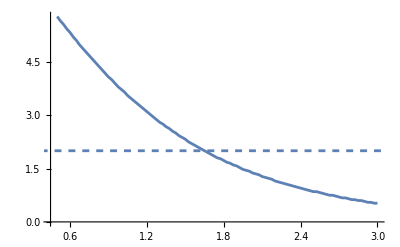

```mathematica
Show[ListPlot[Reverse /@ solAll, Joined->True, PlotRange->All], Plot[2, {x, 0, 10}, PlotStyle -> Dashed]]
```

### Faster version: larger steps and using interpolation

```mathematica
Clear[tab, sol, solAll, probValue];
probValue = probSigma[2];
listk1 = Range[0.5, 3, 0.1];
listm1 = Range[0.4, 6, 0.1];
sol[0] = {arbitraryK, Last @ listm1}; (*Only used for the first step.*)

tab[nk1_] := tab[nk1] = Block[{nm1Previous, nm1Minimal, listm1Relevant},
  nm1Previous = Position[listm1, Last@sol[nk1-1]][[1,1]];
  nm1Minimal = If[nm1Previous - 10 < 1, 1, nm1Previous - 10];
  listm1Relevant = listm1 // Take[#, {nm1Minimal, nm1Previous}] &;
  Table[
    {{listk1[[nk1]], m1}, Abs[probabilityMminApprox[m1, k -> listk1[[nk1]]] - probValue]} , 
    {m1, listm1Relevant}
  ]
];
sol[nk1_] := sol[nk1] = tab[nk1] // SortBy[#, Last][[1,1]] & (*// Echo*);

solAll := solAll = Monitor[Table[sol[nk1], {nk1, Length @ listk1}], nk1];
```

```mathematica
solAll // EchoTiming
```

91.8483

{{0.5,5.8},{0.6,5.3},{0.7,4.9},{0.8,4.4},{0.9,4.1},{1.,3.7},{1.1,3.4},{1.2,3.1},{1.3,2.8},{1.4,2.5},{1.5,2.3},{1.6,2.1},{1.7,1.9},{1.8,1.7},{1.9,1.5},{2.,1.4},{2.1,1.3},{2.2,1.1},{2.3,1.},{2.4,0.9},{2.5,0.8},{2.6,0.8},{2.7,0.7},{2.8,0.6},{2.9,0.6},{3.,0.5}}

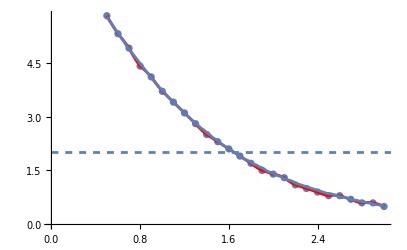

```mathematica
solAllI = Interpolation[solAll, InterpolationOrder->2];
Show[ListPlot[solAll], Plot[solAllI[k], {k, 0.5, 3}, PlotStyle->Red], -Graphics- ]
```